# Lab 2

```mathematica
ClearAll["Global`*"]
```

#### Langevin’s model for Brownian motion

We assign a randomized set of parameters. First, we work with just the randomized parameters ψ(t)=1/k Σ_(i=1)^k cos(Ω t), where k is the number of random values, which we take from a standard normal distribution. It is claimed by the textbook that this function will initially decay, but then display rapid bounded fluctuation. We examine whether this behavior is observed.

```mathematica
k=400;
omegas=RandomVariate[NormalDistribution[],{1,k}][[1]];
```

```mathematica
psi[t_]:=1/k Sum[Cos[omegas[[i]]t],{i,1,k}]
```

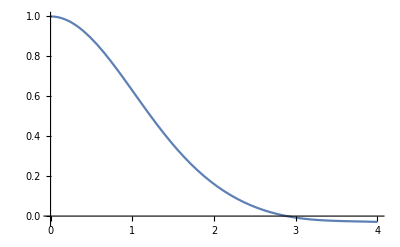

```mathematica
Plot[psi[t],{t,0,4}]
```

We confirm that this function does decay between values 0 and 1.

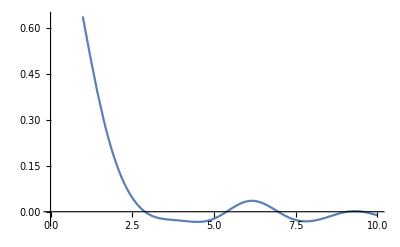

```mathematica
Plot[psi[t],{t,0,10}]
```

Fluctuations occur as expected.

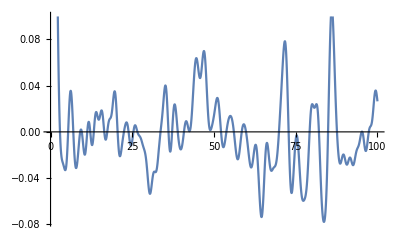

```mathematica
Plot[psi[t],{t,0,100}]
```